```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["Raw/CombCorrect.Error"];
Proc = ConstantArray[0,Length[ErrorData]];
For [i = 1, i <= Length[ErrorData], i++,
	Datum = ErrorData[[i]];
	Proc[[i]] = {#[[1]],Log[#[[2]]/((1-#[[1]])*Datum[[1,2]]+
		#[[1]]*Last[Datum][[2]])]}&/@Datum
]
Save["CombCorrect.Error.Log.Ratio",Proc]
```

```mathematica
(*Get["Raw/ThermoIncorrect.Error"];*)
Get["Raw/CombIncorrect.Error"];
Proc = ConstantArray[0,Length[ErrorData]];
For [i = 1, i <= Length[ErrorData], i++,
	Datum = ErrorData[[i]];
	Proc[[i]] = {#[[1]],#[[2]]/((1-#[[1]])*Datum[[1,2]]+
		#[[1]]*Last[Datum][[2]])}&/@Datum
]
Save["CombIncorrect.Error.Log.Ratio",Proc];
```

```mathematica
Get["Raw/CombCorrect.Times.Unnormalized"]
Time = ConstantArray[0,Length[Raw]];
Vist = ConstantArray[0,Length[Raw]];
For [i = 1, i <= Length[Raw], i++,
	Datum = Raw[[i]];
	Time[[i]] = {#[[1]],Log[#[[2]][[1]]/((1-#[[1]])*Datum[[1,2,1]]+
		#[[1]]*Last[Datum][[2]][[1]])]}&/@Datum;
	Vist[[i]] = {#[[1]],Log[#[[2]][[2]]/((1-#[[1]])*Datum[[1,2,2]]+
		#[[1]]*Last[Datum][[2]][[2]])]}&/@Datum;
]
Save["CombCorrect.Times.Log.Ratio",Time];
Save["CombCorrect.Visits.Log.Ratio",Vist];
```

{{{0.,{6.58309,6.46815}},{0.05,{6.58309,6.46815}},{0.1,{6.58309,6.46815}},{0.15,{6.58309,6.46815}},{0.2,{6.58309,6.46815}},{0.25,{6.58309,6.46815}},{0.3,{6.58309,6.46815}},{0.35,{6.58309,6.46815}},{0.4,{6.58309,6.46815}},{0.45,{6.58309,6.46815}},{0.5,{6.58309,6.46815}},{0.55,{6.58309,6.46815}},{0.6,{6.58309,6.46815}},{0.65,{6.58309,6.46815}},{0.7,{6.58309,6.46815}},{0.75,{6.58309,6.46815}},{0.8,{6.58309,6.46815}},{0.85,{6.58309,6.46815}},{0.9,{6.58309,6.46815}},{0.95,{6.58309,6.46815}},{1.,{6.58309,6.46815}}},{{0.,{18.7909,18.6217}},{0.05,{21.9916,21.8047}},{0.1,{24.7028,24.4391}},{0.15,{27.0053,26.7293}},{0.2,{29.2267,28.8797}},{0.25,{30.8941,30.5203}},{0.3,{32.2198,31.8079}},{0.35,{32.9411,32.4503}},{0.4,{33.1654,32.6898}},{0.45,{32.8109,32.2962}},{0.5,{32.1807,31.7359}},{0.55,{30.9669,30.4197}},{0.6,{29.1136,28.6324}},{0.65,{26.8181,26.2746}},{0.7,{24.683,24.2091}},{0.75,{21.6037,21.2491}},{0.8,{18.677,18.2512}},{0.85,{15.6053,15.256}},{0.9,{12.5441,12.2752}},{0.95,{9.43541,9.19433}},{1.,{6.58309,6.46815}}},{{0.,{54.4295,54.0944}},{0.05,{130.394,129.561}},{0.1,{213.05,211.649}},{0.15,{302.759,300.716}},{0.2,{416.927,414.037}},{0.25,{518.389,514.715}},{0.3,{597.964,593.632}},{0.35,{675.655,670.644}},{0.4,{746.708,740.997}},{0.45,{777.356,771.22}},{0.5,{783.975,777.775}},{0.55,{775.329,768.883}},{0.6,{722.038,715.703}},{0.65,{653.837,648.004}},{0.7,{564.423,558.959}},{0.75,{471.519,466.681}},{0.8,{344.033,339.977}},{0.85,{238.732,235.69}},{0.9,{132.883,130.845}},{0.95,{50.9578,49.7046}},{1.,{6.58309,6.46815}}},{{0.,{157.096,151.52}},{0.05,{1859.69,1793.6}},{0.1,{4592.86,4429.55}},{0.15,{8604.69,8298.64}},{0.2,{13935.,13439.3}},{0.25,{19361.3,18672.3}},{0.3,{24493.2,23621.3}},{0.35,{28988.5,27956.2}},{0.4,{33040.1,31863.1}},{0.45,{35970.,34688.}},{0.5,{37174.7,35849.1}},{0.55,{36804.4,35491.2}},{0.6,{35358.7,34096.3}},{0.65,{31986.6,30843.4}},{0.7,{27465.4,26482.4}},{0.75,{21642.,20865.9}},{0.8,{15847.8,15278.1}},{0.85,{10147.9,9781.54}},{0.9,{5143.09,4955.92}},{0.95,{1564.11,1506.}},{1.,{6.58309,6.46815}}},{{0.,{531.822,418.529}},{0.05,{69481.2,54680.7}},{0.1,{241528.,190080.}},{0.15,{516694.,406634.}},{0.2,{816688.,642731.}},{0.25,{1.20618×10^6,949261.}},{0.3,{1.52448×10^6,1.19978×10^6}},{0.35,{1.85573×10^6,1.46048×10^6}},{0.4,{2.10695×10^6,1.65821×10^6}},{0.45,{2.33445×10^6,1.83727×10^6}},{0.5,{2.41341×10^6,1.89944×10^6}},{0.55,{2.44153×10^6,1.9216×10^6}},{0.6,{2.31019×10^6,1.81826×10^6}},{0.65,{2.08794×10^6,1.64338×10^6}},{0.7,{1.81029×10^6,1.42488×10^6}},{0.75,{1.43788×10^6,1.13181×10^6}},{0.8,{1.01176×10^6,796452.}},{0.85,{684948.,539230.}},{0.9,{307428.,242091.}},{0.95,{93818.5,73923.}},{1.,{6.58309,6.46815}}}}

```mathematica
Get["Raw/CombIncorrect.Times.Unnormalized"];
Time = ConstantArray[0,Length[Raw]];
Vist = ConstantArray[0,Length[Raw]];
For [i = 1, i <= Length[Raw], i++,
	Datum = Raw[[i]];
	Time[[i]] = {#[[1]],Log[#[[2]][[1]]/((1-#[[1]])*Datum[[1,2,1]]+
		#[[1]]*Last[Datum][[2]][[1]])]}&/@Datum;
	Vist[[i]] = {#[[1]],Log[#[[2]][[2]]/((1-#[[1]])*Datum[[1,2,2]]+
		#[[1]]*Last[Datum][[2]][[2]])]}&/@Datum;
]
Save["CombIncorrect.Times.Log.Ratio",Time];
Save["CombIncorrect.Visits.Log.Ratio",Vist];
```

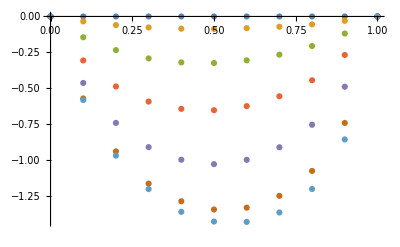

```mathematica
ListPlot[Vist]
```

```mathematica
E^(-1.4)
```

0.246597

```mathematica
Get["Raw/CombIncorrect.Times.Unnormalized"];
Time = ConstantArray[0,Length[Raw]];
Vist = ConstantArray[0,Length[Raw]];
For [i = 1, i <= Length[Raw], i++,
	Datum = Raw[[i]];
	Time[[i]] = {#[[1]],Log[#[[2]][[1]]/((1-#[[1]])*Datum[[1,2,1]]+
		#[[1]]*Last[Datum][[2]][[1]])]}&/@Datum;
	Vist[[i]] = {#[[1]],#[[2]][[2]]}&/@Datum;
]
```

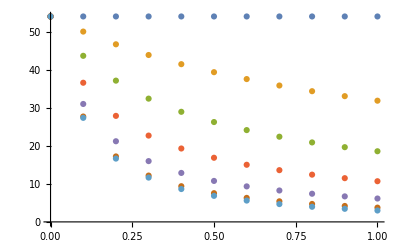

```mathematica
ListPlot[Vist]
```